```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"]
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[b,a],x]
```

Piecewise[{{((1-x)^(-1+a) x^(-1+b))/Beta[b,a], 0<x<1}, {0, True}}]

```mathematica
ClearAll[cd];cd[x_]=Assuming[x>0,FS@Log[PDF[CauchyDistribution[Log[1000],Log[1000]],x]]]
```

-Log[π (x^2-6 x Log[10]+18 Log[10]^2)]+Log[Log[1000]]

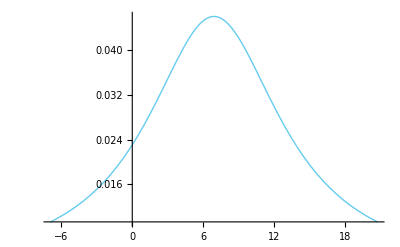

```mathematica
Plot[Exp[cd[lx]],{lx,Log[10^-3],Log[10^9]},PlotRange->Auto]
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
symptoms={{1}};snps={3+{34,82}};
symptomvariants={{0},{1}};snpvariants={{0,0},{0,1},{1,0},{1,1}};
namesymptomvariants={"n","y"};
namesymptoms="";namesnps="";namesnpvariants="";
```

```mathematica
{numsymptoms=Length[symptoms],numsymptomvariants=Length[symptomvariants],numsnps=Length[snps],numsnpvariants=Length[snpvariants],namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}]}
```

{1,2,1,4,{EV_n,EV_y,SD_n,SD_y,post.theta_n,post.theta_y,opt.theta_n,opt.theta_y,max.spread_n,max.spread_y}}

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=cd[Log@t]-Log[t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread]//MF
```

((0.723798 | 0.702726 | 0.740547 | 0.72688
0.276202 | 0.297274 | 0.259453 | 0.27312
0.00739721 | 0.0150239 | 0.0120716 | 0.0229324
0.00739721 | 0.0150239 | 0.0120716 | 0.0229324
2643.67 | 649.67 | 975.67 | 273.67
1008.83 | 274.83 | 341.83 | 102.83
43.6703 | Null | Null | Null
16.8295 | Null | Null | Null
1.39582 | Null | Null | Null
1.39582 | Null | Null | Null))

```mathematica
sdata=data[[;;,Join[symptoms[[1]],snps[[1]]]]];
```

```mathematica
f=Table[Total[Boole/@Table[z==Join[symptomvariant,snpvariant],{z,sdata}]],{symptomvariant,symptomvariants},{snpvariant,snpvariants}]
```

{{1455,1868,503,542},{516,698,224,223}}

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+Total[logpriortheta[t]]];
```

```mathematica
logprob[{1,2}]//N
```

-3569.87

```mathematica
thetas=Array[t,numsymptomvariants]
```

{t[1],t[2]}

```mathematica
thetas=Table[Unique["t"],numsymptomvariants]
```

{t45,t46}

```mathematica
FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{41.0502,16.3425}

```mathematica
FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{-3565.28,{t45→41.0502,t46→16.3425}}

```mathematica
test[[2]]
```

{t45→41.0502,t46→16.3425}

```mathematica
theta=thetas/.FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]][[2]]
```

{{t39,t40}/.{t39,1092},{t39,t40}/.{t40,1661/4}}

```mathematica
fnew=f+theta
```

{{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343}}

```mathematica
nnew=Total[fnew]
```

{2028.39,2623.39,784.393,822.393}

```mathematica
Sequence@@T[T[fnew]/nnew]
```

Sequence[{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032}]

```mathematica
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))]
```

{0.00976638,0.00868929,0.0164497,0.01583}

```mathematica
Sqrt@T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]
```

{{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583}}

```mathematica
Table[Null,numsnpvariants-1,numsymptomvariants]
```

{{Null,Null},{Null,Null},{Null,Null}}

```mathematica
T@Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]
```

{{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
quantities={(*EV*)Sequence@@T[T[fnew]/nnew],(*STD*)Sequence@@Sqrt[T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]],(*(*Quantiles*)Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),*)(*f+theta*)Sequence@@fnew,(*posterior theta*)Sequence@@T[Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]]}
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
spread[q_]:=Max/@Abs@ArrayReshape[Table[(q[[co,x]]-q[[co,y]])/(q[[co+numsymptomvariants,x]]+q[[co+numsymptomvariants,y]]),{co,numsymptomvariants},{x,numsnpvariants-1},{y,x+1,numsnpvariants}],{numsymptomvariants,Binomial[numsnpvariants,2]}]
```

```mathematica
spread[quantities]
```

{1.67685,1.67685}

```mathematica
Join[quantities,T[Join[{spread[quantities]},Table[Null,numsnpvariants-1,numsymptomvariants]]]]
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null},{1.67685,Null,Null,Null},{1.67685,Null,Null,Null}}